# PS 13 — Rania 3.25.2025

## Section 33

```mathematica
(*33.1 Head of output from ListPlot*)
Head[ListPlot[Range[10]]]
```

Graphics

```mathematica
(*33.2*)
Times @@ Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
(*33.3 Use @@@ and Tuples to generate {f[a,a],f[a,b],f[b,a],f[b,b]}.*)
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

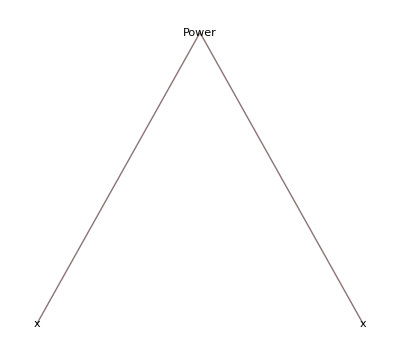
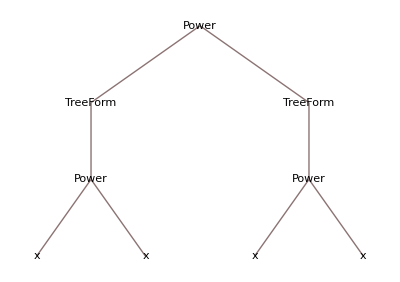
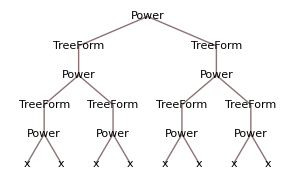
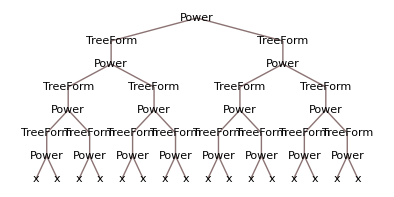
{x,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*33.4 Make a list of expression trees for the results of 4 successive applications of #^#& starting from x.*)
NestList[TreeForm[#^#]&,x,4]
```

```mathematica
(*33.5 Find the unique cases where i^2/(j^2+1) is an integer,with i and j going up to 20.*)
Select[Flatten[Table[i^2/(j^2+1),{i,20},{j,20}]],IntegerQ]
```

{2,8,5,18,32,50,20,10,2,72,98,45,128,17,162,200,80,40,8}

```mathematica
(*33.6 Create a graph that connects successive pairs of numbers in Table[Mod[n^2+n,100],{n,100}]*)
Graph[Rule @@@ Partition[Table[Mod[n^2+n,100],{n,100}],2,1]]
```

-Graphics-

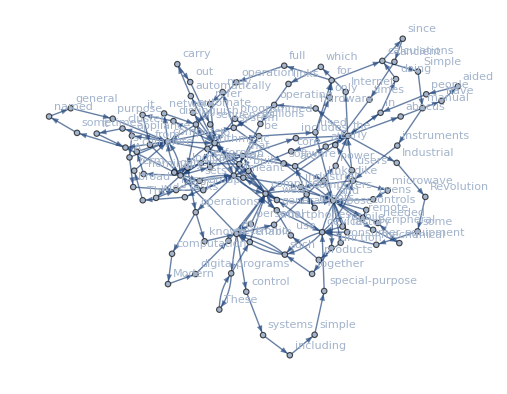

```mathematica
(*33.7 Generate a graph showing which word can follow which in the first 200 words of the Wikipedia article on computers.*)
Graph[Rule @@@ Partition[Take[TextWords[WikipediaData["computers"]],200],2,1],VertexLabels->All]
```

```mathematica
(*33.8 Find a simpler form for f@@#&/@{{1,2},{7,2},{5,4}}.*)
f@@ #&/@{{1,2},{7,2},{5,4}}
f @@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

{f[1,2],f[7,2],f[5,4]}

## Section 34

```mathematica
(*34.1 Make a list, in order,of the number of times each of the digits 0 through 9 occurs in 3^100*)
Values[KeyTake[Counts[IntegerDigits[3^100]],Range[10]-1]]
```

{7,9,9,5,1,5,4,7,1}

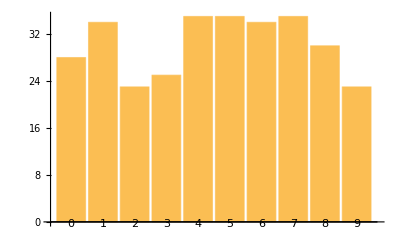

```mathematica
(*34.2 Make a labeled bar chart of the number of times each of the digits 0 through 9 occurs in 2^1000 *)
BarChart[KeyTake[Counts[IntegerDigits[2^1000]], Range[10]-1], ChartLabels->Automatic]
```

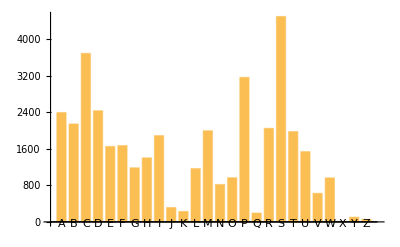

```mathematica
(*34.3Make a labeled bar chart of the number of times each possible first letter occurs in words from WordList[],with all letters made uppercase*)
BarChart[Counts[First/@Characters/@ToUpperCase/@WordList[]], ChartLabels->Automatic]
```

```mathematica
(*34.4Make an association giving the 5 most common first letters of words in WordList[] and their counts.»*)
Reverse[Sort[Counts[First /@ Characters /@ WordList[]]]][[1;;5]]
```

<|s→4499,c→3693,p→3168,d→2433,a→2393|>

```mathematica
(*34.5Find the numerical ratio of the number of occurrences of “q” and “u” in the Wikipedia entry for computers.»*)
(Counts[Flatten[Characters/@TextWords[ WikipediaData["computers"]]]]["q"])/(Counts[Flatten[Characters/@TextWords[ WikipediaData["computers"]]]]["u"])//N

(*#q/#e&@Counts[Flatten[Characters/@TextWords[ WikipediaData["computers"]]]]//N*)
```

0.0400254

```mathematica
(*34.6Find the 10 most common words in ExampleData[{"Text","AliceInWonderland"}]*)
```

```mathematica
Reverse[Sort[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]]]][[1;;10]]//Keys
```

{the,and,a,to,she,of,was,Alice,in,it}